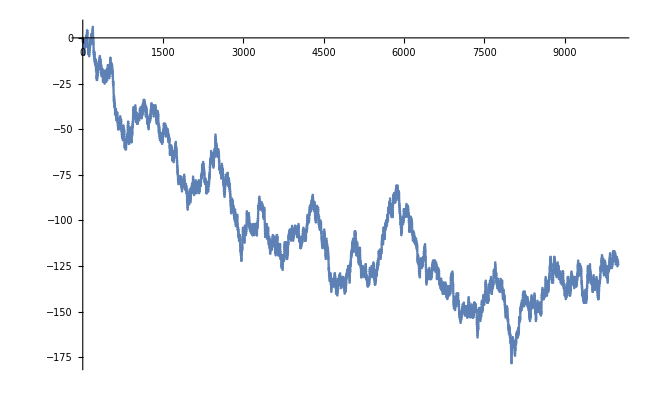

15

```mathematica
n=10000;
y=List[0];
For[i=1,i<=n,i++,
If[RandomInteger[{0,1}]==0,AppendTo[y,y[[i]]+1], AppendTo[y,y[[i]]-1]]
];
ListPlot[y]
Count[y,0]
```